```mathematica
(* CONSTANTS *)
α = 2.1683;
a1 = -0.04531;
a2 = -1.0808;
vlsIndices = Range[50] - 1;

(* GSEH Solution *)
```

```mathematica
(vl[l_] = (l + 0.5) * Pi );
```

```mathematica
vls = Map[vl, vlsIndices];
vlsLength = Length[vls];
```

```mathematica
muns = NSolve[{-BesselJ[1, mu * 6.0] * (BesselY[1, mu * 4.0]/BesselJ[1, mu * 4.0] ) + BesselY[1, mu * 6.0] == 0, 0 <= mu <= 12* Pi}, mu];
munsLength = Length[muns]
```

23

```mathematica
muns = mu/.muns
```

{1.58047,3.14653,4.71569,6.28567,7.85597,9.42643,10.997,12.5676,14.1383,15.709,17.2797,18.8504,20.4211,21.9919,23.5626,25.1334,26.7041,28.2749,29.8457,31.4164,32.9872,34.558,36.1287}

```mathematica
CNFUNC[munN_] =-BesselY[1, munN * 4.0] / BesselJ[1, munN * 4.0];
```

```mathematica
CNS = Map[CNFUNC, muns];
```

```mathematica
λsquare[lVal_,muVal_] :=(lVal^2 + muVal^2)^2
```

```mathematica
λsquared = Transpose[Outer[λsquare, vls, muns]];
```

```mathematica
λsquared [[1,2]]
```

610.312

```mathematica
eu[n_,x_] := (1 / muns[[n]])* (
	a1 * x^2 * (
	CNS[[n]] * BesselJ[2, muns[[n]] * x]
	+ BesselY[2, muns[[n]] * x] 
)+
	a2 * (
	CNS[[n]] * BesselJ[0, muns[[n]] * x]
	+ BesselY[0, muns[[n]] * x]
)
)
```

```mathematica
ed[n_, x_] := -0.5 * x^2 * BesselY[0, muns[[n]] * x] * BesselY[2, muns[[n]] * x] - 0.5 * CNS[[n]]^2 * x^2 * BesselJ[0, muns[[n]] * x] * BesselJ[2, muns[[n]] * x]+ CNS[[n]] * (
0.5 * x^2 * (
BesselJ[0, muns[[n]] * x] - BesselJ[2, muns[[n]] * x]
) * BesselY[0, muns[[n]] * x]
- (1 / muns[[n]]) * x * BesselJ[0, muns[[n]] * x] * BesselY[1, muns[[n]] * x]
)
au[n_]:=eu[n, 6.0] - eu[n, 4.0] 
ad[n_]:=ed[n, 6.0] - ed[n, 4.0]
innerIterate[x_,z_,l_,n_]:=(
((-1)^(l-1) * 2 * au[n])
/
(vls[[l]]*ad[n] * (α^2 -λsquared[[n,l]] ))
)*(CNS[[n]] * BesselJ[1, muns[[n]] * x]+BesselY[1, muns[[n]] *x])*Cos[vls[[l]]*z]
```

```mathematica
psi[x_,z_]:=x *Sum[
innerIterate[x,z,lV,nV], {lV, 1, vlsLength}, {nV, 1, munsLength}
]
```

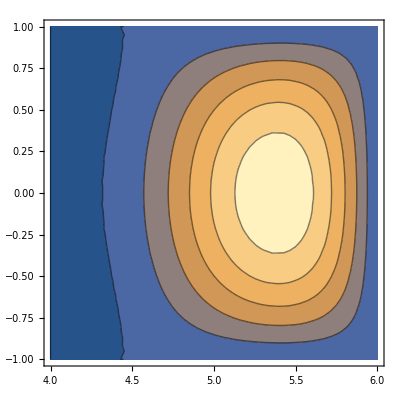

```mathematica
(* Grad-Shafranov Helmholtz Equation*)
ContourPlot[Evaluate[psi[x,z]], {x, 4.0, 6.0}, {z, -1.0, 1.0}]
```

```mathematica
(* Grad-Shafranov Helmholtz Equation*)
(* NOTE: I've made the substitutions for a1 and a2 here to simplify to two equations. *)

(*eq1 = x * D[ (1/x)* D[psi[x,z], x], x] + D[psi[x,z], {z,2}] == -x * jϕ ;*)


eq2 = x * D[ (1/x)* D[psi[x,z], x], x] + D[psi[x,z], {z,2}] == a1 * x^2 - a2 - α^2 * psi[x,z];

eq3 = x * D[ (1/x)* D[psi[x,z], x], x] + D[psi[x,z], {z,2}] - a1 * x^2 + a2 + α^2 * psi[x,z];


(* How do we representing jϕ here? What are B0 and μ0? (in the sense do we know what value we can give them)*)
```

```mathematica
eq3 /. {x -> 5.0, z -> 0.5}
```

-0.854887